```mathematica
SatisfiabilityInstances
```

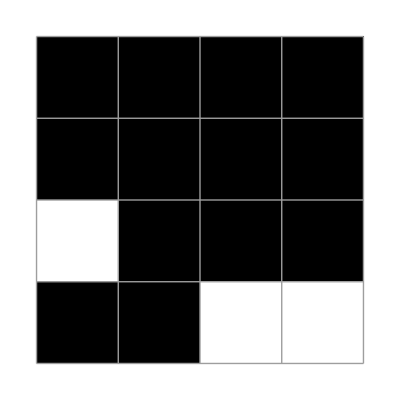
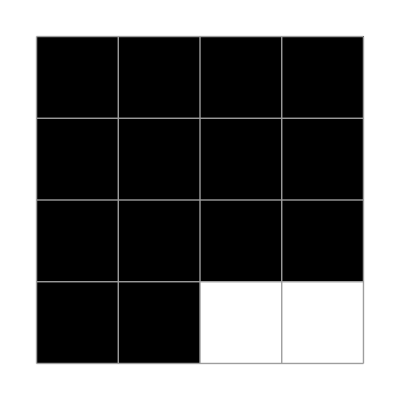
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/04_four_cell.m"];
looker2=plt[({{xNW11, xN11, xN12, xNE12}, {xW11, x11, x12, xE12}, {xW21, x21, x22, xE22}, {xSW21, xS21, xS22, xSE22}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

```mathematica
Implies
```

```mathematica
⇒
```

```mathematica
cnf[x⇒False]
```

CNF | DNF
¬x | ¬x

```mathematica
life44
```

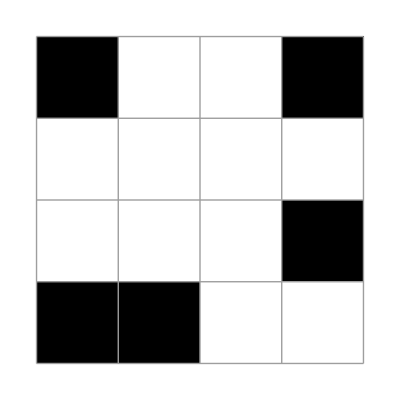
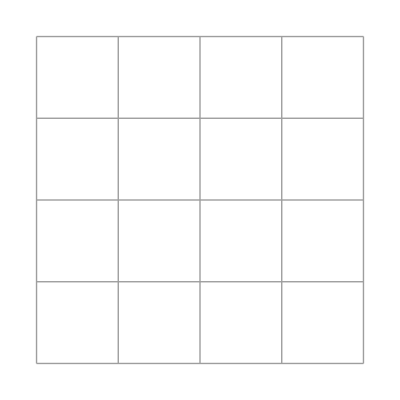
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
X0=({{xNW11, xN11, xN12, xNE12}, {xW11, x11, x12, xE12}, {xW21, x21, x22, xE22}, {xSW21, xS21, xS22, xSE22}})/.endGame[[1]];
plt/@NestList[updateLife2[{4,4}][ #]&,
X0,3]
```